# Doble péndulo

### Derivación de las ecuaciones EL

```mathematica
L = 1/2 l^2(θ1'[t]^2 (m1+m2) + θ2'[t]^2 m2 + 2 m2 θ1'[t] θ2'[t])+g l ((m1+m2)Cos[θ1[t]]+ m2 Cos[θ2[t]]);
```

```mathematica
EulerLagrange[L_,q_]:=Block[{lhs,rhs},
lhs = D[D[L,q'[t]],t];
rhs = D[L,q[t]];
Solve[lhs==rhs,q''[t]]
];
```

```mathematica
EulerLagrange[L,θ1]
```

{{θ1''[t]→(-g m1 Sin[θ1[t]]-g m2 Sin[θ1[t]]-l m2 θ2''[t])/(l (m1+m2))}}

```mathematica
EulerLagrange[L,θ2]
```

{{θ2''[t]→(-g Sin[θ2[t]]-l θ1''[t])/l}}

### Solución numérica

```mathematica
m1=10.0 ;
m2=5;
l=20.0;
g=9.81;
tMax =50;
```

```mathematica
solution = NDSolveValue[
{
θ1''[t]==(-g*( 2*m1+m2 )*Sin[θ1[t]]-m2*g*Sin[θ1[t]-2*θ2[t]]-2*Sin[θ1[t]-θ2[t]]*m2*( l*(θ2'[t]^2 )+( θ1'[t]^2 )*Cos[θ1[t]-θ2[t]] ))/(l*(2*m1+m2-m2*Cos[2*(θ1[t]-θ2[t])])), θ2''[t]==(2*Sin[θ1[t]-θ2[t]]*(g*(m1+m2)*Cos[θ1[t]]+l*((θ2'[t]^2)*m2*Cos[θ1[t]-θ2[t]]+(θ1'[t]^2)*(m1+m2))))/(l*(2*m1+m2-m2*Cos[2*(θ1[t]-θ2[t])])),
θ1[0] == 1, θ2[0] == 0, θ2'[0] == 0, θ1'[0] == 0
},
{θ1[t],θ2[t]},
{t,0,tMax},AccuracyGoal->40
]
```

{InterpolatingFunction[…][t],InterpolatingFunction[…][t]}

```mathematica
r[θ1_,θ2_]:={Sin[θ1]+Sin[θ2],-Cos[θ1]-Cos[θ2]};
r[tp_]:=Apply[r,solution/.t->tp];
```

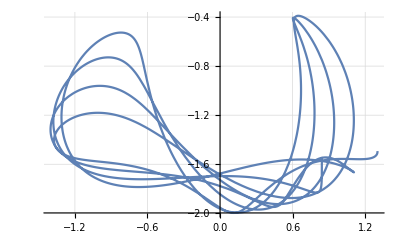

```mathematica
ParametricPlot[r[t],{t,0,tMax},
FrameLabel->{Style["x", 15], Style["y", 15]}, 
GridLines->Automatic
]
```

### Gráfica interactiva

```mathematica
PlotSolution[θ10_,θ20_,tMax_]:=Block[{solution,r},
solution = NDSolveValue[
{
θ1''[t]==(-g*( 2*m1+m2 )*Sin[θ1[t]]-m2*g*Sin[θ1[t]-2*θ2[t]]-2*Sin[θ1[t]-θ2[t]]*m2*( l*(θ2'[t]^2 )+( θ1'[t]^2 )*Cos[θ1[t]-θ2[t]] ))/(l*(2*m1+m2-m2*Cos[2*(θ1[t]-θ2[t])])), θ2''[t]==(2*Sin[θ1[t]-θ2[t]]*(g*(m1+m2)*Cos[θ1[t]]+l*((θ2'[t]^2)*m2*Cos[θ1[t]-θ2[t]]+(θ1'[t]^2)*(m1+m2))))/(l*(2*m1+m2-m2*Cos[2*(θ1[t]-θ2[t])])),
θ1[0] == θ10, θ2[0] == θ20, θ2'[0] == 0, θ1'[0] == 0
},
{θ1[t],θ2[t]},
{t,0,tMax},AccuracyGoal->40
];
r[θ1_,θ2_]:={Sin[θ1]+Sin[θ2],-Cos[θ1]-Cos[θ2]};
r[tp_]:=Apply[r,solution/.t->tp];

ParametricPlot[r[t],{t,0,tMax},
FrameLabel->{Style["x", 15], Style["y", 15]}, 
GridLines->Automatic
]
];
```

```mathematica
PlotSolution[1,0,100]
```

```mathematica
Manipulate[
PlotSolution[θ10,θ20,tMax],
{{θ10,1},-π,π},
{{θ20,0},-π,π},
{{tMax,100},1,1000}
]
```

## Fractal de doble péndulo

La naturaleza caótica del doble péndulo se puede poner en evidencia creando un mapeo dependiente de las condiciones iniciales en el cual se grafíca si al empezar con unas condiciones iniciales θ_(1i) y θ_(2i) se cumple determinado evento. Este evento puede ser por ejemplo que el segundo péndulo de una vuelta, es decir que θ_2 llegue a tener un valor de π. El mapeo resultante tiene una estructura fractal.

```mathematica
DPFrac[θ1i_,θ2i_,tmax_]:=Module[{m1=10.0,m2=10,l=20.0,g=9.81, sol,max},sol = NDSolveValue[{θ1''[t]==(-g*( 2*m1+m2 )*Sin[θ1[t]]-m2*g*Sin[θ1[t]-2*θ2[t]]-2*Sin[θ1[t]-θ2[t]]*m2*( l*(θ2'[t]^2 )+( θ1'[t]^2 )*Cos[θ1[t]-θ2[t]] ))/(l*(2*m1+m2-m2*Cos[2*(θ1[t]-θ2[t])])), θ2''[t]==(2*Sin[θ1[t]-θ2[t]]*(g*(m1+m2)*Cos[θ1[t]]+l*((θ2'[t]^2)*m2*Cos[θ1[t]-θ2[t]]+(θ1'[t]^2)*(m1+m2))))/(l*(2*m1+m2-m2*Cos[2*(θ1[t]-θ2[t])])),
θ1[0] == θ1i, θ2[0] == θ2i, θ2'[0] == 0, θ1'[0] == 0},{θ1,θ2},{t,0,tmax}
];
max = FindMaximum[{sol[[2]][t],0 ≤ t ≤ tmax},t];
Return[If[max[[1]] ≥  π, t /. max [[2]], -1]];
];
Dynamic[θ1i]
Dynamic[θ2i]
DensityPlot[DPFrac[θ1i,θ2i,500],{θ1i,-π,π},{θ2i,-π,π},ColorFunction->"SunsetColors",PlotPoints->50]
```